## Isotope Scattering

```mathematica
(*http://journals.aps.org/prb/pdf/10.1103/PhysRevB.88.144306*)
(*http://journals.aps.org/prb/pdf/10.1103/PhysRevB.27.858*)
```

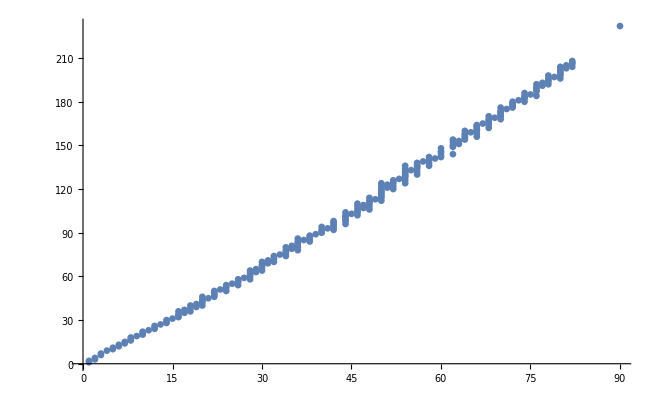

```mathematica
ListPlot[Flatten[Table[Thread[{z,ElementData[z,"StableIsotopes"]}],{z,100}],1]]
```

```mathematica
Table[ElementData[element,"AtomicMass"],{element,1,100,1}]
```

{1.00794 u,4.002602 u,6.941 u,9.012182 u,10.811 u,12.0107 u,14.0067 u,15.9994 u,18.9984032 u,20.1791 u,22.98976928 u,24.305 u,26.9815386 u,28.0855 u,30.973762 u,32.065 u,35.453 u,39.948 u,39.0983 u,40.078 u,44.955912 u,47.867 u,50.9415 u,51.9961 u,54.938045 u,55.845 u,58.933195 u,58.6934 u,63.546 u,65.38 u,69.723 u,72.63 u,74.9216 u,78.96 u,79.904 u,83.798 u,85.4678 u,87.62 u,88.90585 u,91.224 u,92.90638 u,95.96 u,98. u,101.07 u,102.9055 u,106.42 u,107.8682 u,112.411 u,114.818 u,118.71 u,121.76 u,127.6 u,126.90447 u,131.293 u,132.9054519 u,137.327 u,138.90547 u,140.116 u,140.90765 u,144.242 u,145. u,150.36 u,151.964 u,157.25 u,158.92535 u,162.5 u,164.93032 u,167.259 u,168.93421 u,173.054 u,174.9668 u,178.49 u,180.94788 u,183.84 u,186.207 u,190.23 u,192.217 u,195.084 u,196.966569 u,200.59 u,204.3833 u,207.2 u,208.9804 u,209. u,210. u,222. u,223. u,226. u,227. u,232.03806 u,231.03586 u,238.02891 u,237. u,244. u,243. u,247. u,247. u,251. u,252. u,257. u}

```mathematica
isotopeAverageMasses=Table[Total@Table[IsotopeData[StringJoin[ElementData[element][[2]],ToString@ElementData[element,"StableIsotopes"][[i]]],"IsotopeAbundance"]*IsotopeData[StringJoin[ElementData[element][[2]],ToString@ElementData[element,"StableIsotopes"][[i]]],"MassNumber"],{i,1,ElementData[element,"StableIsotopes"]//Length}]//N,{element,1,80,1}];
```

```mathematica
isotopeAverageMasses
```

{1.00015,4.,6.9241,9.,10.802,12.0111,14.0037,16.0044,19.,20.1877,23.,24.3202,27.,28.1086,31.,32.0925,35.4846,39.9853,39.13,40.0272,45.,47.9183,50.8725,52.0554,55.,55.9099,59.,58.7596,63.6166,65.4682,69.7978,66.7672,75.,71.8835,79.9862,83.8873,61.3445,87.7104,89.,88.6304,93.,86.3955,0.,101.16,103.,106.511,107.963,90.011,4.8477,118.808,121.856,41.6725,127.,131.387,133.,137.422,138.875,140.21,141.,101.653,0.,111.778,152.044,157.024,159.,162.569,165.,167.327,169.,173.099,170.468,178.262,180.978,183.891,69.19,187.321,192.254,195.087,197.,200.609}

```mathematica
isotopeAtoms=Table[atom,{atom,1,80}];
```

```mathematica
isotopeMasses=Table[Table[IsotopeData[StringJoin[ElementData[element][[2]],ToString@ElementData[element,"StableIsotopes"][[i]]],"IsotopeAbundance"]*IsotopeData[StringJoin[ElementData[element][[2]],ToString@ElementData[element,"StableIsotopes"][[i]]],"MassNumber"],{i,1,ElementData[element,"StableIsotopes"]//Length}]//N,{element,1,80,1}];
```

```mathematica
isotopeAbundances=Table[Table[IsotopeData[StringJoin[ElementData[element][[2]],ToString@ElementData[element,"StableIsotopes"][[i]]],"IsotopeAbundance"],{i,1,ElementData[element,"StableIsotopes"]//Length}]//N,{element,1,80,1}];
```

```mathematica
isotopeDegeneracies=Map[Length,isotopeAbundances,1]
```

{2,2,2,1,2,2,2,3,1,3,1,3,1,3,1,4,2,3,2,5,1,5,1,4,1,4,1,5,2,5,2,4,1,5,2,6,1,4,1,4,1,6,0,7,1,6,2,6,1,10,2,5,1,9,1,7,1,4,1,5,0,5,2,6,1,7,1,6,1,7,1,5,1,5,1,6,2,5,1,7}

```mathematica
ListPlot[isotopeDegeneracies]
```

```mathematica
isotopeSymbol=Table[Table[IsotopeData[StringJoin[ElementData[element][[2]],ToString@ElementData[element,"StableIsotopes"][[i]]],"Symbol"],{i,1,ElementData[element,"StableIsotopes"]//Length}]//N,{element,1,80,1}];
```

```mathematica
isotopeVariances=Table[Total[Table[isotopeAbundances[[atom]][[isotope]]*(1-isotopeMasses[[atom]][[isotope]]/isotopeAverageMasses[[atom]])^2,{isotope,1,isotopeMasses[[atom]]//Length}]],{atom,1,isotopeAverageMasses//Length}]
```

{0.00015,1.37×10^-6,0.0702418,0.,0.159012,0.0109776,0.00364667,0.00237773,0.,0.0871896,0.,0.20461,0.,0.0773739,0.,0.0486358,0.183698,0.00398901,0.0627822,0.0286665,0.,0.278947,0.,0.162183,0.,0.081142,0.,0.267665,0.213296,0.44329,0.23983,0.456026,0.,0.379543,0.249991,0.428719,0.,0.170895,0.,0.436678,0.,0.602465,0,0.647908,1.2326×10^-32,0.611353,0.249683,0.43572,0.,0.643307,0.244818,0.136488,0.,0.63421,0.,0.29436,0.,0.103941,0.,0.398246,0,0.395719,0.249531,0.641865,0.,0.575268,0.,0.553214,0.,0.626454,0.,0.563129,0.,0.542293,0.,0.508317,0.233877,0.507058,1.2326×10^-32,0.64104}

```mathematica
isotopeVarianceParameter=Table[Total[Table[isotopeAbundances[[atom]][[isotope]]*(Sqrt[isotopeAverageMasses[[atom]]]-isotopeMasses[[atom]][[isotope]]/Sqrt[isotopeAverageMasses[[atom]]])^2,{isotope,1,isotopeMasses[[atom]]//Length}]],{atom,1,isotopeAverageMasses//Length}]
```

{0.000150022,5.47999×10^-6,0.486361,0.,1.71765,0.131853,0.0510668,0.0380541,7.88861×10^-31,1.76016,7.88861×10^-31,4.97614,0.,2.17487,7.88861×10^-31,1.56084,6.51844,0.159502,2.45667,1.14744,0.,13.3667,7.86889×10^-31,8.44249,0.,4.53665,3.15544×10^-30,15.7279,13.5692,29.0214,16.7396,30.4476,3.15544×10^-30,27.2829,19.9959,35.9641,5.69321×10^-31,14.9893,3.15544×10^-30,38.703,0.,52.0503,0,65.5422,0.,65.1158,26.9566,39.2196,0.,76.4298,29.8325,5.68781,3.15544×10^-30,83.3268,3.15544×10^-30,40.4515,3.1526×10^-30,14.5735,3.15544×10^-30,40.4829,0,44.2326,37.9397,100.788,0.,93.5208,0.,92.5677,0.,108.439,3.07372×10^-30,100.384,0.,99.7227,0.,95.2182,44.9638,98.9204,3.15544×10^-30,128.599}

```mathematica
normalIsotopeVariances=isotopeVariances*100/Max@isotopeVariances;
normalIsotopeVariances1=isotopeVariances*100/Max@isotopeVariances/100;
normalIsotopeVarianceParameters=isotopeVarianceParameter*100/Max@isotopeVarianceParameter
normalIsotopeVariancesParameters1=Round[normalIsotopeVarianceParameters]/100
```

{0.00011666,4.26131×10^-6,0.378201,0.,1.33567,0.102531,0.0397102,0.0295913,6.13429×10^-31,1.36872,6.13429×10^-31,3.86952,0.,1.69121,6.13429×10^-31,1.21373,5.06883,0.124031,1.91034,0.892265,0.,10.3941,6.11895×10^-31,6.565,0.,3.52776,2.45372×10^-30,12.2302,10.5516,22.5674,13.017,23.6765,2.45372×10^-30,21.2155,15.5491,27.9661,4.42712×10^-31,11.6558,2.45372×10^-30,30.0959,0.,40.475,0.,50.9665,0.,50.635,20.9618,30.4977,0.,59.4328,23.1981,4.42292,2.45372×10^-30,64.796,2.45372×10^-30,31.4556,2.45151×10^-30,11.3326,2.45372×10^-30,31.4801,0.,34.3958,29.5024,78.3743,0.,72.723,0.,71.9819,0.,84.3236,2.39016×10^-30,78.0602,0.,77.5457,0.,74.0429,34.9644,76.9218,2.45372×10^-30,100.}

{0,0,0,0,1/100,0,0,0,0,1/100,0,1/25,0,1/50,0,1/100,1/20,0,1/50,1/100,0,1/10,0,7/100,0,1/25,0,3/25,11/100,23/100,13/100,6/25,0,21/100,4/25,7/25,0,3/25,0,3/10,0,2/5,0,51/100,0,51/100,21/100,3/10,0,59/100,23/100,1/25,0,13/20,0,31/100,0,11/100,0,31/100,0,17/50,3/10,39/50,0,73/100,0,18/25,0,21/25,0,39/50,0,39/50,0,37/50,7/20,77/100,0,1}

#### Plot raw Isotope scattering vs atomic mass

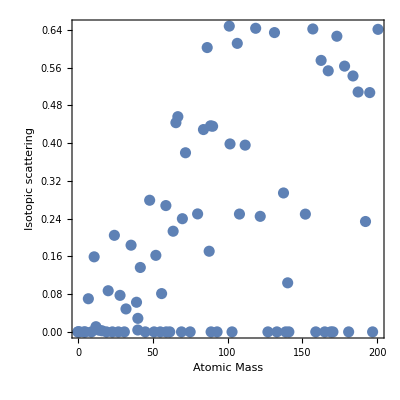

```mathematica
plotOptsAvMass={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameLabel->{Style["Atomic Mass",20],Style["Isotopic scattering",20]},PlotRange->All,AspectRatio->1,PlotStyle->PointSize[0.02]};
ListPlot[Transpose[{isotopeAverageMasses,isotopeVariances}],Evaluate@plotOptsAvMass]
```

```mathematica
[Transpose[{isotopeAverageMasses,isotopeVariances}]]
```

{{3592.77,6.37172},{6.37172,0.0521705}}

#### Plot raw isotope scattering vs atomic degeneracy

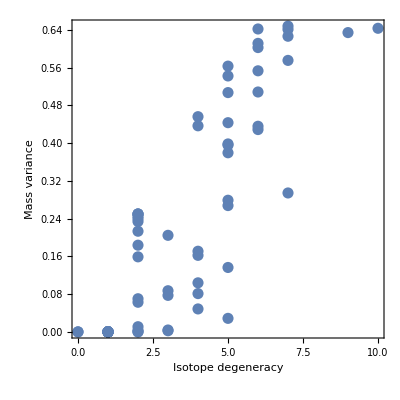

```mathematica
plotOptsDegen={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameLabel->{Style["Isotope degeneracy",20],Style["Mass variance",20]},PlotRange->All,AspectRatio->1,PlotStyle->PointSize[0.02]};
ListPlot[Transpose[{isotopeDegeneracies,isotopeVariances}],Evaluate@plotOptsDegen]
```

#### Plot raw isotope scattering mass variance vs atomic number

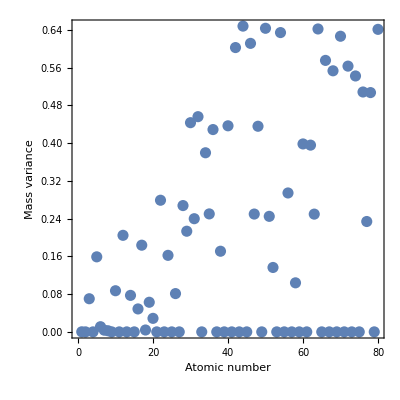

```mathematica
plotOptsAtoms={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameLabel->{Style["Atomic number",20],Style["Mass variance",20]},PlotRange->All,AspectRatio->1,PlotStyle->PointSize[0.02]};
ListPlot[Transpose[{isotopeAtoms,isotopeVariances}],Evaluate@plotOptsAtoms]
```

#### Plot normalised isotope scattering vs atomic number

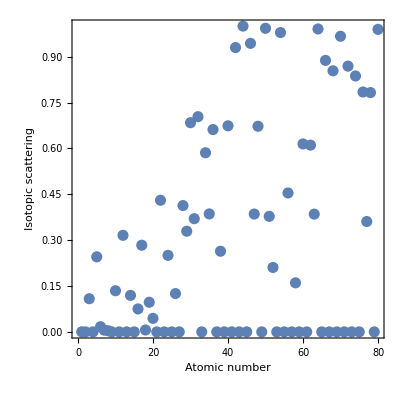

```mathematica
plotOptsAtomsN={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameLabel->{Style["Atomic number",20],Style["Isotopic scattering",20]},PlotRange->All,AspectRatio->1,PlotStyle->PointSize[0.02]};
ListPlot[Transpose[{isotopeAtoms,normalIsotopeVariances1}],Evaluate@plotOptsAtomsN]
```

## Normalised isotope scattering parameter

#### vs atomic number

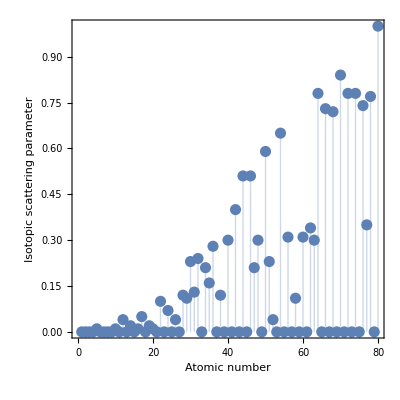

```mathematica
plotOptsAtomsN1={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameLabel->{Style["Atomic number",20],Style["Isotopic scattering parameter",20]},PlotRange->All,AspectRatio->1,PlotStyle->PointSize[0.02],Filling->Axis};
ListPlot[Transpose[{isotopeAtoms,normalIsotopeVariancesParameters1}],Evaluate@plotOptsAtomsN1]
```

```mathematica
vs isotopic degeneracy
```

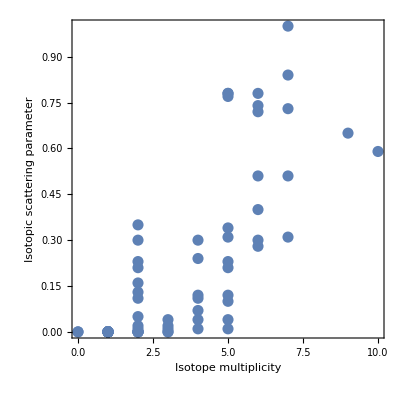

```mathematica
plotOptsDegen1={FrameTicksStyle->20,Frame->True,ImageSize->400,FrameLabel->{Style["Isotope multiplicity",20],Style["Isotopic scattering parameter",20]},PlotRange->All,AspectRatio->1,PlotStyle->PointSize[0.02]};
ListPlot[Transpose[{isotopeDegeneracies,normalIsotopeVariancesParameters1}],Evaluate@plotOptsDegen1]
```

#### Isotope multiplicity wordcloud

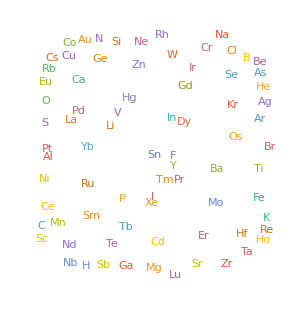
```mathematica
WordCloud@Table[Table[ElementData[element,"Symbol"],{i,1,isotopeDegeneracies[[element]]}],{element,1,80}]
-Graphics-
```

```mathematica
Round@normalIsotopeVariances
```

{0,0,11,0,25,2,1,0,0,13,0,32,0,12,0,8,28,1,10,4,0,43,0,25,0,13,0,41,33,68,37,70,0,59,39,66,0,26,0,67,0,93,0,100,0,94,39,67,0,99,38,21,0,98,0,45,0,16,0,61,0,61,39,99,0,89,0,85,0,97,0,87,0,84,0,78,36,78,0,99}

#### Raw isotope variance wordcloud

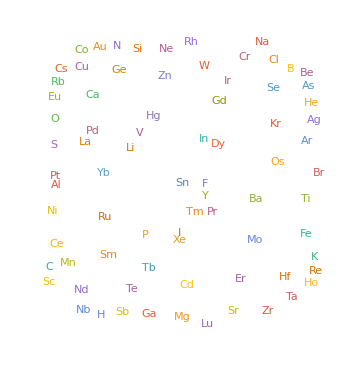
```mathematica
WordCloud@Table[Table[ElementData[element,"Symbol"],{i,1,Round@normalIsotopeVariances[[element]]}],{element,1,80}]
-Graphics-
```

#### Isotope variance parameter wordcloud

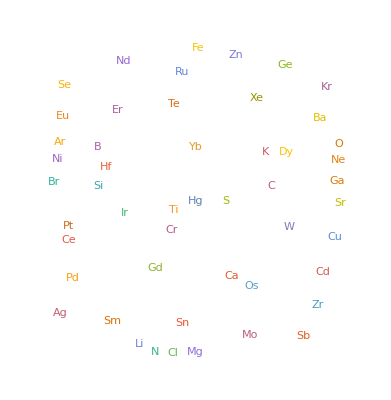

```mathematica
WordCloud@Table[Table[ElementData[element,"Symbol"],{i,1,Round@100*normalIsotopeVarianceParameters[[element]]}],{element,1,80}]
```

{AtomicMass,AtomicNumber,BindingEnergy,BranchingRatios,DaughterNuclides,DecayEnergies,DecayModes,DecayModeSymbols,DecayProducts,ExcitedStateEnergies,ExcitedStateHalfLives,ExcitedStateLifetimes,ExcitedStateParities,ExcitedStateSpins,ExcitedStateWidths,FullSymbol,HalfLife,IsotopeAbundance,Lifetime,MagneticMoment,MassExcess,MassNumber,Memberships,Name,NeutronNumber,Parity,QuadrupoleMoment,QuantumStatistics,Spin,Stable,StandardName,Symbol,Width}

0.0012

5.7×10^25 s

180

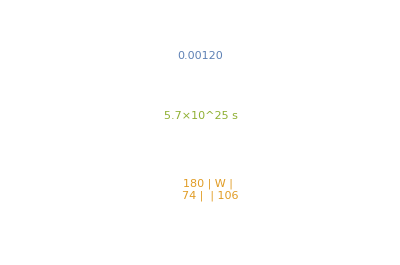

```mathematica
IsotopeData["Tungsten180","Properties"]
IsotopeData["Tungsten180","IsotopeAbundance"]
IsotopeData["Tungsten180","HalfLife"]
IsotopeData["Tungsten180","MassNumber"]
WordCloud[{IsotopeData["Tungsten180","FullSymbol"],IsotopeData["Tungsten180","IsotopeAbundance"],IsotopeData["Tungsten180","HalfLife"]}]
```

```mathematica
CorrelationTest[Transpose[{isotopeAtoms,normalIsotopeVariancesParameters1}]]
```

0.000119571